```mathematica
MyFolderX=NotebookDirectory[]
```

/Users/shawnliang/Desktop/Data & Code/Midterm/

```mathematica
(* Store filepath (string) of PersonData_ALL_N_354842_ALL.txt file in FilePathX *)
FilePathX=StringJoin[MyFolderX,"PersonData_ALL_N_354842_ALL.txt"]
```

/Users/shawnliang/Desktop/Data & Code/Midterm/PersonData_ALL_N_354842_ALL.txt

```mathematica
(* Import Data > Store in the local variabe "Din" *)
Din=Import[FilePathX,"CSV",CharacterEncoding-> "UTF8","TextDelimiters"->"\""];
```

```mathematica
NDataALL = Length[Din]
```

354842

```mathematica
1.Time Period Between 1890s and 1900s  -- Woman Occupation Types in the United States [ ~20 Years before World War II ]
```

```mathematica
HeaderX={"Name","FullName","Gender","NationalityCountries","BirthDate","DeathDate","BirthPlace","DeathPlace","Occupation","Wives","Husbands"};

(* Choose from Dataset to obtain 1890s-1900s indivduals, and cleaning the data by getting rid of NotAvailable data, and rounding the year to decades.*)
```

```mathematica
DinFirst = Reap[For[i = 1,i<=NDataALL, i++,
If[(ToExpression[StringDrop[Din[[i]][[5]],-7]]*10 == 1890 || (ToExpression[StringDrop[Din[[i]][[5]],-7]]*10 ==1900)) &&
(Din[[i]][[4]]== "UnitedStates")&&
 (Din[[i]][[3]]== "Female")&&
(Din[[i]][[-3]]!= "NotAvailable")
, Sow[Din[[i]]]
]]][[2]][[1]];
DinFirst[[1;;3]]
Length[DinFirst]
```

{{Aleta Freel,NotAvailable,Female,UnitedStates,1907-06-17,1935-12-07,JerseyCity;NewJersey;UnitedStates,LosAngeles;California;UnitedStates,actor,NotAvailable,RossAlexander::vp78n},{Addie McPhail,NotAvailable,Female,UnitedStates,1905-07-15,2003-04-14,WhitePlains;Kentucky;UnitedStates,NotAvailable,actor,NotAvailable,FattyArbuckle::4h657;Lindsay_McPhail},{Adela Rogers St. Johns,NotAvailable,Female,UnitedStates,1894-05-20,1988-08-10,LosAngeles;California;UnitedStates,ArroyoGrande;California;UnitedStates,writer,NotAvailable,Ivan_St._Johns;Dick_Irving_Hyland}}

885

```mathematica
2. Count Different Birth Years and Occupation Types from Woman People Dataset
```

```mathematica
DBirthYearFirst = DinFirst
DBirthYearFirst= Reap[For[i = 1, i <= Length[DBirthYearFirst], i++,
Sow[ToExpression[StringDrop[DBirthYearFirst[[i]][[5]],-7]]*10]]][[2]][[1]];
```

{{Aleta Freel,NotAvailable,Female,UnitedStates,1907-06-17,1935-12-07,JerseyCity;NewJersey;UnitedStates,LosAngeles;California;UnitedStates,actor,NotAvailable,RossAlexander::vp78n},883,{Fern Emmett,NotAvailable,Female,UnitedStates,1896-03-22,1946-09-03,NewYork;NewYork;UnitedStates,NotAvailable,actor,NotAvailable,Henry Roquemore}}
 |  |  |  |

```mathematica
(*The Amount of in this dataset *)
Length[DBirthYearFirst]
DBirthYearFirst[[1;;10]]
```

885

{1900,1900,1890,1900,1900,1900,1890,1900,1900,1890}

```mathematica
DOccupationsFirst= DinFirst
DOccupationsFirst= Reap[For[i = 1, i <= Length[DOccupationsFirst], i++,
Sow[DOccupationsFirst[[i]][[-3]]]]][[2]][[1]];
```

{{Aleta Freel,NotAvailable,Female,UnitedStates,1907-06-17,1935-12-07,JerseyCity;NewJersey;UnitedStates,LosAngeles;California;UnitedStates,actor,NotAvailable,RossAlexander::vp78n},883,{Fern Emmett,NotAvailable,Female,UnitedStates,1896-03-22,1946-09-03,NewYork;NewYork;UnitedStates,NotAvailable,actor,NotAvailable,Henry Roquemore}}
 |  |  |  |

```mathematica
(* Combine Year and Occupation data sets,
sepereate the occupations for when an indidual has more than one *)
```

```mathematica
DOC = Transpose[{DBirthYearFirst,DOccupationsFirst}];
DOC[[1;;2]]

SplitDOC = Reap[For[i = 1,i≤Length[DOC],i++,
s = StringSplit[DOC[[i,2]],";"];

For[j = 1,j≤ Length[s],j++,
Sow[{DOC[[i,1]],s[[j]]}]
]

]][[2]][[1]];
```

{{1900,actor},{1900,actor}}

```mathematica
(* Tally the data and get the repeated times in dataset for years and occupations)
```

```mathematica
YDOC = Tally[Flatten[SplitDOC[[All,1]]]];
TableForm[YDOC]
```

1890 | 3933
1900 | 4809

```mathematica
3) Define Bipartite matrix associating people with their interests - use a sorted interest-index
```

```mathematica
(* Only take the first 200 data from the split data, because the larger the dataset, the messier the graphs.
This way we can have a more clear overall analysis.*)
NewDOC = SplitDOC[[1;;200]];
NewDOC[[-1]]
```

{1890,actor}

```mathematica
NewODOC = Tally[Flatten[NewDOC[[All,2]]]];
TableForm[NewODOC]
Length[NewODOC]
(* Below are the first 200 occupations and number of times they appear in 1890s - 1900s *)
```

actor | 79
writer | 7
singer | 13
performer | 2
teacher | 5
military | 1
athlete | 7
dancer | 3
academy award winner | 2
critic | 2
religious | 1
screenwriter | 3
playwright | 1
novelist | 9
model | 1
author | 11
comedian | 1
judge | 1
artist | 6
scientist | 1
film producer | 1
lecturer | 1
activist | 1
lyricist | 2
composer | 3
community organizer | 1
television presenter | 1
journalist | 1
songwriter | 3
psychologist | 1
aviator | 3
vocalist | 2
musician | 4
photographer | 1
academy award nominee | 2
educator | 1
philanthropist | 1
astrophysicist | 1
tennis player | 1
politician | 2
painter | 1
poet | 1
historian | 1
cartoonist | 1
singer/songwriter | 1
producer | 1
rapper | 1
illustrator | 1
diplomat | 1
retired | 1
famous by association | 1

51

```mathematica
(* Create "dictionary" which maps a person/interest name to an index *)
Clear[MapYeari]
For[i=1,i≤Length[YDOC],i++,MapYeari[YDOC[[i,1]]]=i; ];
```

```mathematica
MapYeari[YDOC[[1,1]]]
MapYeari[YDOC[[-1,1]]]
```

1

2

```mathematica
Clear[MapOccupationj];
For[i=1,i≤Length[NewODOC],i++,MapOccupationj[NewODOC[[i]][[1]]]=i; ];
MapOccupationj["cartoonist"]
```

44

```mathematica
64
```

64

```mathematica
Length[NewODOC]
```

51

```mathematica
(* Calculate the bipartite association matrix *)
YearOccupationMatrix=Array[0&,{Length[YDOC],Length[NewODOC]}];
For[i=1,i≤Length[NewDOC],i++,
nInt=MapOccupationj[NewDOC[[i,2]]];
mInt=MapYeari[NewDOC[[i,1]]];
YearOccupationMatrix[[mInt]][[nInt]]=YearOccupationMatrix[[mInt]][[nInt]]+1;
];

MatrixForm[YearOccupationMatrix]
```

(47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
32 | 5 | 7 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 6 | 1 | 2 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
Show[Colorize[YearOccupationMatrix],ImageSize-> 400,AspectRatio-> 1]
```

-Graphics-

```mathematica
4) Define Year-Year and Occupation-Occupation association matrix using bipartite projection method
```

```mathematica
(* Year-Year association matrix *)
YearYearBipartiteProj=YearOccupationMatrix.Transpose[YearOccupationMatrix];
Length[YearYearBipartiteProj]
For[i=1,i≤ Length[YearYearBipartiteProj],i++, YearYearBipartiteProj[[i]][[i]]=0;] 
(* Delete diagonal elements *)
MatrixForm[YearYearBipartiteProj] (* Number of occupations are the same in these years*)
```

2

(0 | 1609
1609 | 0)

```mathematica
(* Occupation-Occupation association matrix *)
OccupationOccupationBipartiteProj=Transpose[YearOccupationMatrix].YearOccupationMatrix;
Length[OccupationOccupationBipartiteProj]
For[i=1,i≤ Length[OccupationOccupationBipartiteProj],i++, OccupationOccupationBipartiteProj[[i]][[i]]=0;] 
(* Delete diagonal elements *)

(* Display Matrix of first 20 occupaton to occupation *)
MatrixForm[OccupationOccupationBipartiteProj]
```

51

(0 | 254 | 506 | 94 | 220 | 47 | 329 | 126 | 94 | 94 | 32 | 111 | 47 | 333 | 32 | 487 | 47 | 47 | 207 | 47 | 32 | 47 | 47 | 94 | 141 | 32 | 47 | 47 | 141 | 47 | 126 | 79 | 188 | 32 | 64 | 47 | 47 | 32 | 47 | 79 | 47 | 47 | 32 | 47 | 47 | 47 | 47 | 47 | 47 | 32 | 47
254 | 0 | 47 | 4 | 13 | 2 | 14 | 9 | 4 | 4 | 5 | 12 | 2 | 36 | 5 | 28 | 2 | 2 | 27 | 2 | 5 | 2 | 2 | 4 | 6 | 5 | 2 | 2 | 6 | 2 | 9 | 7 | 8 | 5 | 10 | 2 | 2 | 5 | 2 | 7 | 2 | 2 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 2
506 | 47 | 0 | 12 | 31 | 6 | 42 | 19 | 12 | 12 | 7 | 20 | 6 | 60 | 7 | 68 | 6 | 6 | 41 | 6 | 7 | 6 | 6 | 12 | 18 | 7 | 6 | 6 | 18 | 6 | 19 | 13 | 24 | 7 | 14 | 6 | 6 | 7 | 6 | 13 | 6 | 6 | 7 | 6 | 6 | 6 | 6 | 6 | 6 | 7 | 6
94 | 4 | 12 | 0 | 8 | 2 | 14 | 4 | 4 | 4 | 0 | 2 | 2 | 6 | 0 | 18 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 4 | 6 | 0 | 2 | 2 | 6 | 2 | 4 | 2 | 8 | 0 | 0 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2
220 | 13 | 31 | 8 | 0 | 4 | 28 | 9 | 8 | 8 | 1 | 6 | 4 | 18 | 1 | 38 | 4 | 4 | 9 | 4 | 1 | 4 | 4 | 8 | 12 | 1 | 4 | 4 | 12 | 4 | 9 | 5 | 16 | 1 | 2 | 4 | 4 | 1 | 4 | 5 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4
47 | 2 | 6 | 2 | 4 | 0 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
329 | 14 | 42 | 14 | 28 | 7 | 0 | 14 | 14 | 14 | 0 | 7 | 7 | 21 | 0 | 63 | 7 | 7 | 7 | 7 | 0 | 7 | 7 | 14 | 21 | 0 | 7 | 7 | 21 | 7 | 14 | 7 | 28 | 0 | 0 | 7 | 7 | 0 | 7 | 7 | 7 | 7 | 0 | 7 | 7 | 7 | 7 | 7 | 7 | 0 | 7
126 | 9 | 19 | 4 | 9 | 2 | 14 | 0 | 4 | 4 | 1 | 4 | 2 | 12 | 1 | 20 | 2 | 2 | 7 | 2 | 1 | 2 | 2 | 4 | 6 | 1 | 2 | 2 | 6 | 2 | 5 | 3 | 8 | 1 | 2 | 2 | 2 | 1 | 2 | 3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2
94 | 4 | 12 | 4 | 8 | 2 | 14 | 4 | 0 | 4 | 0 | 2 | 2 | 6 | 0 | 18 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 4 | 6 | 0 | 2 | 2 | 6 | 2 | 4 | 2 | 8 | 0 | 0 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2
94 | 4 | 12 | 4 | 8 | 2 | 14 | 4 | 4 | 0 | 0 | 2 | 2 | 6 | 0 | 18 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 4 | 6 | 0 | 2 | 2 | 6 | 2 | 4 | 2 | 8 | 0 | 0 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2
32 | 5 | 7 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 6 | 1 | 2 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
111 | 12 | 20 | 2 | 6 | 1 | 7 | 4 | 2 | 2 | 2 | 0 | 1 | 15 | 2 | 13 | 1 | 1 | 11 | 1 | 2 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 3 | 1 | 4 | 3 | 4 | 2 | 4 | 1 | 1 | 2 | 1 | 3 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 0 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
333 | 36 | 60 | 6 | 18 | 3 | 21 | 12 | 6 | 6 | 6 | 15 | 3 | 0 | 6 | 39 | 3 | 3 | 33 | 3 | 6 | 3 | 3 | 6 | 9 | 6 | 3 | 3 | 9 | 3 | 12 | 9 | 12 | 6 | 12 | 3 | 3 | 6 | 3 | 9 | 3 | 3 | 6 | 3 | 3 | 3 | 3 | 3 | 3 | 6 | 3
32 | 5 | 7 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 6 | 0 | 2 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
487 | 28 | 68 | 18 | 38 | 9 | 63 | 20 | 18 | 18 | 2 | 13 | 9 | 39 | 2 | 0 | 9 | 9 | 19 | 9 | 2 | 9 | 9 | 18 | 27 | 2 | 9 | 9 | 27 | 9 | 20 | 11 | 36 | 2 | 4 | 9 | 9 | 2 | 9 | 11 | 9 | 9 | 2 | 9 | 9 | 9 | 9 | 9 | 9 | 2 | 9
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
207 | 27 | 41 | 2 | 9 | 1 | 7 | 7 | 2 | 2 | 5 | 11 | 1 | 33 | 5 | 19 | 1 | 1 | 0 | 1 | 5 | 1 | 1 | 2 | 3 | 5 | 1 | 1 | 3 | 1 | 7 | 6 | 4 | 5 | 10 | 1 | 1 | 5 | 1 | 6 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 1 | 1 | 5 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
32 | 5 | 7 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 6 | 1 | 2 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
94 | 4 | 12 | 4 | 8 | 2 | 14 | 4 | 4 | 4 | 0 | 2 | 2 | 6 | 0 | 18 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 0 | 6 | 0 | 2 | 2 | 6 | 2 | 4 | 2 | 8 | 0 | 0 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2
141 | 6 | 18 | 6 | 12 | 3 | 21 | 6 | 6 | 6 | 0 | 3 | 3 | 9 | 0 | 27 | 3 | 3 | 3 | 3 | 0 | 3 | 3 | 6 | 0 | 0 | 3 | 3 | 9 | 3 | 6 | 3 | 12 | 0 | 0 | 3 | 3 | 0 | 3 | 3 | 3 | 3 | 0 | 3 | 3 | 3 | 3 | 3 | 3 | 0 | 3
32 | 5 | 7 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 6 | 1 | 2 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 0 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 0 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
141 | 6 | 18 | 6 | 12 | 3 | 21 | 6 | 6 | 6 | 0 | 3 | 3 | 9 | 0 | 27 | 3 | 3 | 3 | 3 | 0 | 3 | 3 | 6 | 9 | 0 | 3 | 3 | 0 | 3 | 6 | 3 | 12 | 0 | 0 | 3 | 3 | 0 | 3 | 3 | 3 | 3 | 0 | 3 | 3 | 3 | 3 | 3 | 3 | 0 | 3
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 0 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
126 | 9 | 19 | 4 | 9 | 2 | 14 | 5 | 4 | 4 | 1 | 4 | 2 | 12 | 1 | 20 | 2 | 2 | 7 | 2 | 1 | 2 | 2 | 4 | 6 | 1 | 2 | 2 | 6 | 2 | 0 | 3 | 8 | 1 | 2 | 2 | 2 | 1 | 2 | 3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2
79 | 7 | 13 | 2 | 5 | 1 | 7 | 3 | 2 | 2 | 1 | 3 | 1 | 9 | 1 | 11 | 1 | 1 | 6 | 1 | 1 | 1 | 1 | 2 | 3 | 1 | 1 | 1 | 3 | 1 | 3 | 0 | 4 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
188 | 8 | 24 | 8 | 16 | 4 | 28 | 8 | 8 | 8 | 0 | 4 | 4 | 12 | 0 | 36 | 4 | 4 | 4 | 4 | 0 | 4 | 4 | 8 | 12 | 0 | 4 | 4 | 12 | 4 | 8 | 4 | 0 | 0 | 0 | 4 | 4 | 0 | 4 | 4 | 4 | 4 | 0 | 4 | 4 | 4 | 4 | 4 | 4 | 0 | 4
32 | 5 | 7 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 6 | 1 | 2 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
64 | 10 | 14 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 2 | 4 | 0 | 12 | 2 | 4 | 0 | 0 | 10 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
32 | 5 | 7 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 6 | 1 | 2 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
79 | 7 | 13 | 2 | 5 | 1 | 7 | 3 | 2 | 2 | 1 | 3 | 1 | 9 | 1 | 11 | 1 | 1 | 6 | 1 | 1 | 1 | 1 | 2 | 3 | 1 | 1 | 1 | 3 | 1 | 3 | 2 | 4 | 1 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
32 | 5 | 7 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 6 | 1 | 2 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1
32 | 5 | 7 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 6 | 1 | 2 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
47 | 2 | 6 | 2 | 4 | 1 | 7 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 9 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 4 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0)

```mathematica
(* Degree Distribution *)
DegreeX=Total[Sign[#]]&/@OccupationOccupationBipartiteProj
```

{50,50,50,41,50,41,41,50,41,41,20,50,41,50,20,50,41,41,50,41,20,41,41,41,41,20,41,41,41,41,50,50,41,20,20,41,41,20,41,50,41,41,20,41,41,41,41,41,41,20,41}

```mathematica
5) WeightedAdjacencyGraph[ ]
```

```mathematica
mat=Replace[OccupationOccupationBipartiteProj,0->Infinity,{2}]; (*  0s represented by infinity in WeightedAdjacencyGraph[ ] *)
OName=NewODOC[[All,1]];

(* Set Labels : The "keys" for each node will be the name stored in OName *)
NameFontSizeX=20;
NodeColorX=Black;
LabelsetBlack=Table[OName[[i]]->Placed[ Style[OName[[i]],FontFamily->"Helvetica",NameFontSizeX,NodeColorX],Center],{i,Length[OName]}]
```

{actor→Placed[actor,Center],writer→Placed[writer,Center],singer→Placed[singer,Center],performer→Placed[performer,Center],teacher→Placed[teacher,Center],military→Placed[military,Center],athlete→Placed[athlete,Center],dancer→Placed[dancer,Center],academy award winner→Placed[academy award winner,Center],critic→Placed[critic,Center],religious→Placed[religious,Center],screenwriter→Placed[screenwriter,Center],playwright→Placed[playwright,Center],novelist→Placed[novelist,Center],model→Placed[model,Center],author→Placed[author,Center],comedian→Placed[comedian,Center],judge→Placed[judge,Center],artist→Placed[artist,Center],scientist→Placed[scientist,Center],film producer→Placed[film producer,Center],lecturer→Placed[lecturer,Center],activist→Placed[activist,Center],lyricist→Placed[lyricist,Center],composer→Placed[composer,Center],community organizer→Placed[community organizer,Center],television presenter→Placed[television presenter,Center],journalist→Placed[journalist,Center],songwriter→Placed[songwriter,Center],psychologist→Placed[psychologist,Center],aviator→Placed[aviator,Center],vocalist→Placed[vocalist,Center],musician→Placed[musician,Center],photographer→Placed[photographer,Center],academy award nominee→Placed[academy award nominee,Center],educator→Placed[educator,Center],philanthropist→Placed[philanthropist,Center],astrophysicist→Placed[astrophysicist,Center],tennis player→Placed[tennis player,Center],politician→Placed[politician,Center],painter→Placed[painter,Center],poet→Placed[poet,Center],historian→Placed[historian,Center],cartoonist→Placed[cartoonist,Center],singer/songwriter→Placed[singer/songwriter,Center],producer→Placed[producer,Center],rapper→Placed[rapper,Center],illustrator→Placed[illustrator,Center],diplomat→Placed[diplomat,Center],retired→Placed[retired,Center],famous by association→Placed[famous by association,Center]}

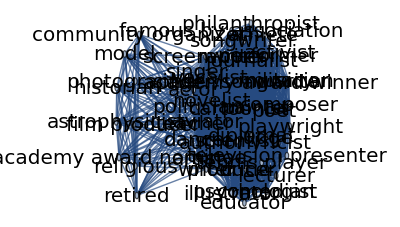

```mathematica
(* Plot Network - an ugly mess *)
g=WeightedAdjacencyGraph[OName,mat,VertexLabels->LabelsetBlack]
```

```mathematica
Clustering Coefficients - to what degree are neighbors connected?
```

```mathematica
(* Global - Network-level characteristic: What fraction of possible triangles (1st order cycle) exist in the network *)
N[GlobalClusteringCoefficient[g]]
```

0.920995

```mathematica
(* Local - Node-level characteristic: What fraction of possible triangles (1st order cycle) exist in the network *)LClusteringCoeffX=N[LocalClusteringCoefficient[g]]
Mean[LClusteringCoeffX]
N[MeanClusteringCoefficient[g]] (* Gives same result as above *)
```

{0.779592,0.779592,0.779592,1.,0.779592,1.,1.,0.779592,1.,1.,1.,0.779592,1.,0.779592,1.,0.779592,1.,1.,0.779592,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.779592,0.779592,1.,1.,1.,1.,1.,1.,1.,0.779592,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

0.948139

0.948139

```mathematica
Length[LClusteringCoeffX]
```

51

```mathematica
Length[OName]
```

51

```mathematica
Sort[Thread[Rule[OName,LClusteringCoeffX]],#1[[2]]>#2[[2]]&]
```

{famous by association→1.,retired→1.,diplomat→1.,illustrator→1.,rapper→1.,producer→1.,singer/songwriter→1.,cartoonist→1.,historian→1.,poet→1.,painter→1.,tennis player→1.,astrophysicist→1.,philanthropist→1.,educator→1.,academy award nominee→1.,photographer→1.,musician→1.,psychologist→1.,songwriter→1.,journalist→1.,television presenter→1.,community organizer→1.,composer→1.,lyricist→1.,activist→1.,lecturer→1.,film producer→1.,scientist→1.,judge→1.,comedian→1.,model→1.,playwright→1.,religious→1.,critic→1.,academy award winner→1.,athlete→1.,military→1.,performer→1.,politician→0.779592,vocalist→0.779592,aviator→0.779592,artist→0.779592,author→0.779592,novelist→0.779592,screenwriter→0.779592,dancer→0.779592,teacher→0.779592,singer→0.779592,writer→0.779592,actor→0.779592}

{{50,0.779592},{50,0.779592},{50,0.779592},{41,1.},{50,0.779592},{41,1.},{41,1.},{50,0.779592},{41,1.},{41,1.},{20,1.},{50,0.779592},{41,1.},{50,0.779592},{20,1.},{50,0.779592},{41,1.},{41,1.},{50,0.779592},{41,1.},{20,1.},{41,1.},{41,1.},{41,1.},{41,1.},{20,1.},{41,1.},{41,1.},{41,1.},{41,1.},{50,0.779592},{50,0.779592},{41,1.},{20,1.},{20,1.},{41,1.},{41,1.},{20,1.},{41,1.},{50,0.779592},{41,1.},{41,1.},{20,1.},{41,1.},{41,1.},{41,1.},{41,1.},{41,1.},{41,1.},{20,1.},{41,1.}}

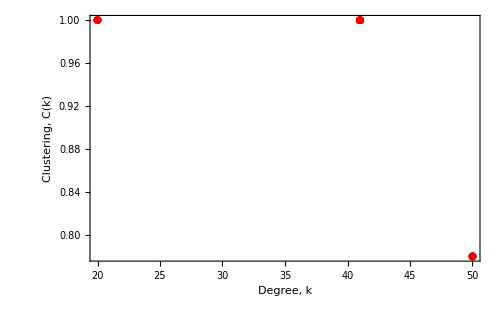

```mathematica
DegreeClusteringX=Thread[{DegreeX,LClusteringCoeffX}]

ListPlot[DegreeClusteringX,
PlotRange-> All,
PlotStyle->Directive[Red,10],
LabelStyle -> Directive[Black,FontSize->20,FontFamily-> "Helvetica"],
Frame->True,
ImageSize->{500,Automatic},
FrameLabel->{"Degree, k","Clustering, C(k)"},
ImageSize->500]
```

```mathematica
Improve network visualization layout
```

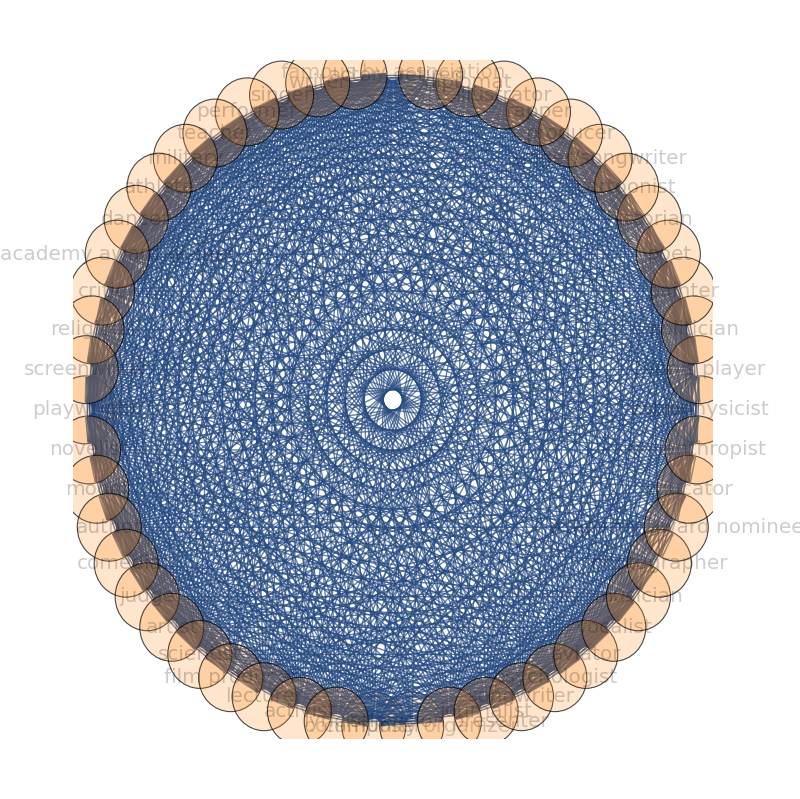

```mathematica
Circlesize=0.05;
r=Array[Circlesize&,Length[OName]]; (* Circle radius list *)

g=WeightedAdjacencyGraph[OName,mat,VertexLabels->LabelsetBlack,VertexSize->Scaled[.10],VertexStyle->Directive[Orange,Opacity[.2]],GraphLayout->{"CircularEmbedding"} ,ImageSize->800]
```

```mathematica
6) Modify the link color and thickness
```

```mathematica
(* AbsoluteOptions[ ]: gives the absolute settings of options specified in an expression such as a graphics object. *)
gEdWe=AbsoluteOptions[g,EdgeWeight][[All,2]][[1]]  (* Get list of edge weights associated with each edge *)
Max[gEdWe]
```

{254,506,94,220,47,329,126,94,94,32,111,47,333,32,487,47,47,207,47,32,47,47,94,141,32,47,47,141,47,126,79,188,32,64,47,47,32,47,79,47,47,32,47,47,47,47,47,47,32,47,47,4,13,2,14,9,4,4,5,12,2,36,5,28,2,2,27,2,5,2,2,4,6,5,2,2,6,2,9,7,8,5,10,2,2,5,2,7,2,2,5,2,2,2,2,2,2,5,2,12,31,6,42,19,12,12,7,20,6,60,7,68,6,6,41,6,7,6,6,12,18,7,6,6,18,6,19,13,24,7,14,6,6,7,6,13,6,6,7,6,6,6,6,6,6,7,6,8,2,14,4,4,4,2,2,6,18,2,2,2,2,2,2,4,6,2,2,6,2,4,2,8,2,2,2,2,2,2,2,2,2,2,2,2,2,4,28,9,8,8,1,6,4,18,1,38,4,4,9,4,1,4,4,8,12,1,4,4,12,4,9,5,16,1,2,4,4,1,4,5,4,4,1,4,4,4,4,4,4,1,4,7,2,2,2,1,1,3,9,1,1,1,1,1,1,2,3,1,1,3,1,2,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,14,14,14,7,7,21,63,7,7,7,7,7,7,14,21,7,7,21,7,14,7,28,7,7,7,7,7,7,7,7,7,7,7,7,7,4,4,1,4,2,12,1,20,2,2,7,2,1,2,2,4,6,1,2,2,6,2,5,3,8,1,2,2,2,1,2,3,2,2,1,2,2,2,2,2,2,1,2,4,2,2,6,18,2,2,2,2,2,2,4,6,2,2,6,2,4,2,8,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,6,18,2,2,2,2,2,2,4,6,2,2,6,2,4,2,8,2,2,2,2,2,2,2,2,2,2,2,2,2,2,6,1,2,5,1,1,1,1,1,2,1,1,1,1,1,15,2,13,1,1,11,1,2,1,1,2,3,2,1,1,3,1,4,3,4,2,4,1,1,2,1,3,1,1,2,1,1,1,1,1,1,2,1,3,9,1,1,1,1,1,1,2,3,1,1,3,1,2,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,6,39,3,3,33,3,6,3,3,6,9,6,3,3,9,3,12,9,12,6,12,3,3,6,3,9,3,3,6,3,3,3,3,3,3,6,3,2,5,1,1,1,1,1,2,1,1,1,1,9,9,19,9,2,9,9,18,27,2,9,9,27,9,20,11,36,2,4,9,9,2,9,11,9,9,2,9,9,9,9,9,9,2,9,1,1,1,1,1,2,3,1,1,3,1,2,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,3,1,2,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,1,2,3,5,1,1,3,1,7,6,4,5,10,1,1,5,1,6,1,1,5,1,1,1,1,1,1,5,1,1,1,2,3,1,1,3,1,2,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,3,1,1,3,1,2,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,3,1,2,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,6,2,2,6,2,4,2,8,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,9,3,6,3,12,3,3,3,3,3,3,3,3,3,3,3,3,3,1,1,1,2,1,1,1,1,1,3,1,2,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,3,6,3,12,3,3,3,3,3,3,3,3,3,3,3,3,3,2,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,3,8,1,2,2,2,1,2,3,2,2,1,2,2,2,2,2,2,1,2,4,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,4,4,4,4,4,4,4,4,4,4,4,4,4,2,1,1,1,1,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

506

```mathematica
(* Use linear transform to rescale edge weight values to be from 0 to 1 *)
gEdWe=Rescale[gEdWe,{0,Max[gEdWe]},{0,1}]
```

{127/253,1,47/253,10/23,47/506,329/506,63/253,47/253,47/253,16/253,111/506,47/506,333/506,16/253,487/506,47/506,47/506,9/22,47/506,16/253,47/506,47/506,47/253,141/506,16/253,47/506,47/506,141/506,47/506,63/253,79/506,94/253,16/253,32/253,47/506,47/506,16/253,47/506,79/506,47/506,47/506,16/253,47/506,47/506,47/506,47/506,47/506,47/506,16/253,47/506,47/506,2/253,13/506,1/253,7/253,9/506,2/253,2/253,5/506,6/253,1/253,18/253,5/506,14/253,1/253,1/253,27/506,1/253,5/506,1/253,1/253,2/253,3/253,5/506,1/253,1/253,3/253,1/253,9/506,7/506,4/253,5/506,5/253,1/253,1/253,5/506,1/253,7/506,1/253,1/253,5/506,1/253,1/253,1/253,1/253,1/253,1/253,5/506,1/253,6/253,31/506,3/253,21/253,19/506,6/253,6/253,7/506,10/253,3/253,30/253,7/506,34/253,3/253,3/253,41/506,3/253,7/506,3/253,3/253,6/253,9/253,7/506,3/253,3/253,9/253,3/253,19/506,13/506,12/253,7/506,7/253,3/253,3/253,7/506,3/253,13/506,3/253,3/253,7/506,3/253,3/253,3/253,3/253,3/253,3/253,7/506,3/253,4/253,1/253,7/253,2/253,2/253,2/253,1/253,1/253,3/253,9/253,1/253,1/253,1/253,1/253,1/253,1/253,2/253,3/253,1/253,1/253,3/253,1/253,2/253,1/253,4/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,2/253,14/253,9/506,4/253,4/253,1/506,3/253,2/253,9/253,1/506,19/253,2/253,2/253,9/506,2/253,1/506,2/253,2/253,4/253,6/253,1/506,2/253,2/253,6/253,2/253,9/506,5/506,8/253,1/506,1/253,2/253,2/253,1/506,2/253,5/506,2/253,2/253,1/506,2/253,2/253,2/253,2/253,2/253,2/253,1/506,2/253,7/506,1/253,1/253,1/253,1/506,1/506,3/506,9/506,1/506,1/506,1/506,1/506,1/506,1/506,1/253,3/506,1/506,1/506,3/506,1/506,1/253,1/506,2/253,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,7/253,7/253,7/253,7/506,7/506,21/506,63/506,7/506,7/506,7/506,7/506,7/506,7/506,7/253,21/506,7/506,7/506,21/506,7/506,7/253,7/506,14/253,7/506,7/506,7/506,7/506,7/506,7/506,7/506,7/506,7/506,7/506,7/506,7/506,7/506,2/253,2/253,1/506,2/253,1/253,6/253,1/506,10/253,1/253,1/253,7/506,1/253,1/506,1/253,1/253,2/253,3/253,1/506,1/253,1/253,3/253,1/253,5/506,3/506,4/253,1/506,1/253,1/253,1/253,1/506,1/253,3/506,1/253,1/253,1/506,1/253,1/253,1/253,1/253,1/253,1/253,1/506,1/253,2/253,1/253,1/253,3/253,9/253,1/253,1/253,1/253,1/253,1/253,1/253,2/253,3/253,1/253,1/253,3/253,1/253,2/253,1/253,4/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,3/253,9/253,1/253,1/253,1/253,1/253,1/253,1/253,2/253,3/253,1/253,1/253,3/253,1/253,2/253,1/253,4/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,3/253,1/506,1/253,5/506,1/506,1/506,1/506,1/506,1/506,1/253,1/506,1/506,1/506,1/506,1/506,15/506,1/253,13/506,1/506,1/506,1/46,1/506,1/253,1/506,1/506,1/253,3/506,1/253,1/506,1/506,3/506,1/506,2/253,3/506,2/253,1/253,2/253,1/506,1/506,1/253,1/506,3/506,1/506,1/506,1/253,1/506,1/506,1/506,1/506,1/506,1/506,1/253,1/506,3/506,9/506,1/506,1/506,1/506,1/506,1/506,1/506,1/253,3/506,1/506,1/506,3/506,1/506,1/253,1/506,2/253,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,3/253,39/506,3/506,3/506,3/46,3/506,3/253,3/506,3/506,3/253,9/506,3/253,3/506,3/506,9/506,3/506,6/253,9/506,6/253,3/253,6/253,3/506,3/506,3/253,3/506,9/506,3/506,3/506,3/253,3/506,3/506,3/506,3/506,3/506,3/506,3/253,3/506,1/253,5/506,1/506,1/506,1/506,1/506,1/506,1/253,1/506,1/506,1/506,1/506,9/506,9/506,19/506,9/506,1/253,9/506,9/506,9/253,27/506,1/253,9/506,9/506,27/506,9/506,10/253,1/46,18/253,1/253,2/253,9/506,9/506,1/253,9/506,1/46,9/506,9/506,1/253,9/506,9/506,9/506,9/506,9/506,9/506,1/253,9/506,1/506,1/506,1/506,1/506,1/506,1/253,3/506,1/506,1/506,3/506,1/506,1/253,1/506,2/253,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/253,3/506,1/506,1/506,3/506,1/506,1/253,1/506,2/253,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,5/506,1/506,1/506,1/253,3/506,5/506,1/506,1/506,3/506,1/506,7/506,3/253,2/253,5/506,5/253,1/506,1/506,5/506,1/506,3/253,1/506,1/506,5/506,1/506,1/506,1/506,1/506,1/506,1/506,5/506,1/506,1/506,1/506,1/253,3/506,1/506,1/506,3/506,1/506,1/253,1/506,2/253,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/253,1/506,1/506,1/506,1/506,1/506,1/253,3/506,1/506,1/506,3/506,1/506,1/253,1/506,2/253,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/253,3/506,1/506,1/506,3/506,1/506,1/253,1/506,2/253,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,3/253,1/253,1/253,3/253,1/253,2/253,1/253,4/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,1/253,3/506,3/506,9/506,3/506,3/253,3/506,6/253,3/506,3/506,3/506,3/506,3/506,3/506,3/506,3/506,3/506,3/506,3/506,3/506,3/506,1/506,1/506,1/506,1/253,1/506,1/506,1/506,1/506,1/506,3/506,1/506,1/253,1/506,2/253,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,3/506,1/506,1/253,1/506,2/253,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,3/506,3/253,3/506,6/253,3/506,3/506,3/506,3/506,3/506,3/506,3/506,3/506,3/506,3/506,3/506,3/506,3/506,1/253,1/506,2/253,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,3/506,4/253,1/506,1/253,1/253,1/253,1/506,1/253,3/506,1/253,1/253,1/506,1/253,1/253,1/253,1/253,1/253,1/253,1/506,1/253,2/253,1/506,1/253,1/506,1/506,1/506,1/506,1/253,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,2/253,2/253,2/253,2/253,2/253,2/253,2/253,2/253,2/253,2/253,2/253,2/253,2/253,1/253,1/506,1/506,1/506,1/506,1/253,1/253,1/253,1/253,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506,1/506}

```mathematica
(* Adjust the link properties *)
ThicknessBoost=8;
OpacityFactor=1; (* 1.15, 1, 1.1*)
RedGreenFactor=-1; (* 1 = Green, -1 = Red *)

(* Thread together the links with their modified color, opacity, and thickness values defined by gEdWe *)
(* The &/@gEdWe means that everywhere that there is a # in the Thread function it will use the corresponding list element in gEdWe *)
ModifiedEdgePropertiesX=
Thread[Rule[EdgeList[g],Directive[ColorData["RedGreenSplit"][Rescale[#,{-1*RedGreenFactor,1 *RedGreenFactor}]],Opacity[(OpacityFactor*#)],AbsoluteThickness[ThicknessBoost*#]]&/@gEdWe]];
Take[ModifiedEdgePropertiesX,3]
```

{actor<->writer→Directive[RGBColor[1., 0.5299012173913044, 0.5299012173913044],Opacity[127/253],AbsoluteThickness[1016/253]],actor<->singer→Directive[RGBColor[1., 0., 0.],Opacity[1],AbsoluteThickness[8]],actor<->performer→Directive[RGBColor[1., 0.8261200632411068, 0.8261200632411068],Opacity[47/253],AbsoluteThickness[376/253]]}

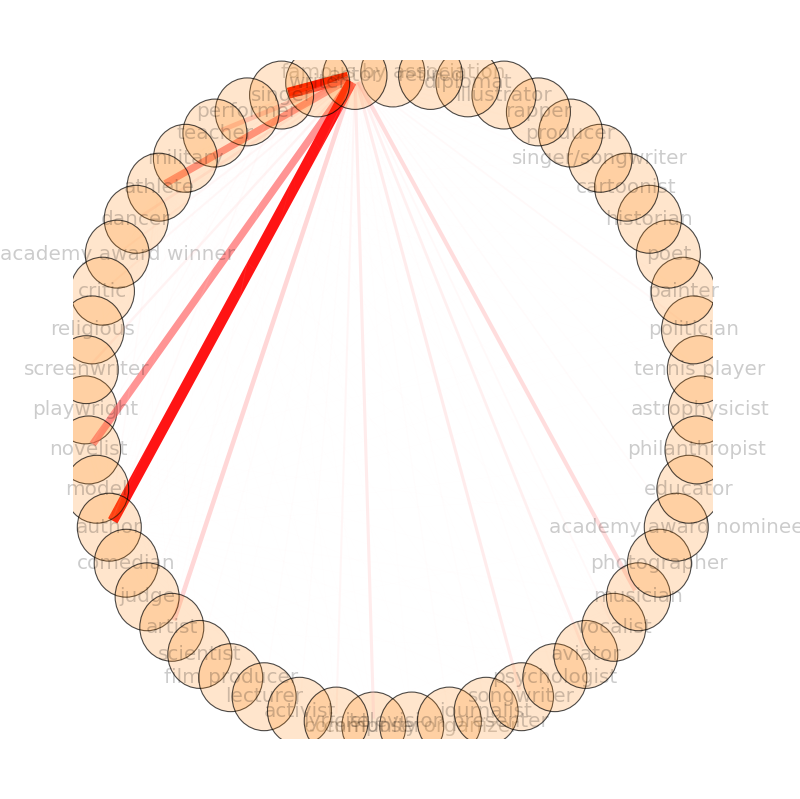

```mathematica
(* Adjust just one option stored in the graph g *)
g=SetProperty[g,EdgeStyle->ModifiedEdgePropertiesX];

Gfin=Show[g,ImagePadding->{{100,100},{100,100}}]
```